```mathematica
ClearAll["Global`*"];
SeedRandom[];

(* ==========================================================*)
(*1. 并发暴胀引擎 (完全原生 Union 去重，无人工排序干预)*)
(* ==========================================================*)
StepEvolution[g_Graph,window_]:=Module[{allEdges,activeEdges,nActive,usedEdges,updates,tempE1,tempE2,x,y,z,wCounter,newVertices,newActive,newFrozen,remainingEdges},allEdges=EdgeList[g];
activeEdges=RandomSample[Cases[allEdges,_UndirectedEdge]];
nActive=Length[activeEdges];
If[nActive<2,Return[{g,0}]];
usedEdges={};updates={};
Do[tempE1=activeEdges[[i]];
If[!MemberQ[usedEdges,tempE1],Do[tempE2=activeEdges[[j]];
If[!MemberQ[usedEdges,tempE2]&&Length[Intersection[List@@tempE1,List@@tempE2]]==1,AppendTo[updates,{tempE1,tempE2}];
AppendTo[usedEdges,tempE1];AppendTo[usedEdges,tempE2];
Break[];],{j,i+1,Min[i+window,nActive]}]],{i,1,nActive}];
If[Length[updates]==0,Return[{g,0}]];
wCounter=Max[VertexList[g]];
newVertices={};newActive={};newFrozen={};
Do[y=Intersection[List@@pair[[1]],List@@pair[[2]]][[1]];
x=Complement[List@@pair[[1]],{y}][[1]];
z=Complement[List@@pair[[2]],{y}][[1]];
wCounter++;
AppendTo[newVertices,wCounter];
newActive=Join[newActive,{UndirectedEdge[x,z],UndirectedEdge[x,wCounter],UndirectedEdge[wCounter,z]}];
newFrozen=Join[newFrozen,{DirectedEdge[x,y],DirectedEdge[y,z]}];,{pair,updates}];
remainingEdges=Complement[allEdges,Flatten[updates]];
{Graph[Union[Join[VertexList[g],newVertices]],Union[Join[remainingEdges,newActive,newFrozen]]],Length[updates]}];

(* ==========================================================*)
(*2. 并发宇宙演化采集 (40 步)*)
(* ==========================================================*)
Print[Style["[1/3] 正在点燃并发暴胀宇宙... (目标: 40步)",Blue,Bold]];
universe=CompleteGraph[6];
steps=200;
widthData={};

Monitor[Do[{universe,concurrentCount}=StepEvolution[universe,50];
If[concurrentCount>0,activeNodes=Union[Flatten[List@@@Cases[EdgeList[universe],_UndirectedEdge]]];
If[Length[activeNodes]>1,dists=(GraphDistance[universe,1,#]&/@activeNodes);
AppendTo[widthData,{i,StandardDeviation[Select[dists,NumericQ]]}];];];,{i,1,steps}],ProgressIndicator[i,{0,steps}]];

(* ==========================================================*)
(*3. 提取最终的能量分布 (形成波包)*)
(* ==========================================================*)
Print[Style["[2/3] 宇宙停止暴胀，正在扫描空间前沿能量分布...",Blue,Bold]];

finalActiveNodes=Union[Flatten[List@@@Cases[EdgeList[universe],_UndirectedEdge]]];
finalDists=Select[(GraphDistance[universe,1,#]&/@finalActiveNodes),NumericQ];

plotWavePacket=Histogram[finalDists,Automatic,"ProbabilityDensity",ChartStyle->LightBlue,Frame->True,FrameLabel->{"Topological Distance (r)","Energy Density"},PlotLabel->Style["Wave Packet Energy Distribution",14,Bold],GridLines->{Automatic,Automatic},ImageSize->450];

(* ==========================================================*)
(*4. 离散对数周期色散检验 (残差雪花)*)
(* ==========================================================*)
Print[Style["[3/3] 正在执行离散色散拟合...",Blue,Bold]];

If[Length[widthData]>20,cutoffStep=10;
adultData=Select[widthData,#[[1]]>cutoffStep&];
w0Init=adultData[[1,2]];
discreteModel=Sqrt[w0^2+(k*t^alpha)^2]*(1+a*Sin[omega*Log[t]+phi]);
nlmDiscrete=Check[NonlinearModelFit[adultData,{discreteModel,k>0&&0.8<alpha<1.2&&a>0},{{w0,w0Init},{k,0.5},{alpha,1.0},{a,0.01},{omega,15},{phi,0}},t,MaxIterations->1500,Method->"NMinimize"],$Failed];
plotSnowflake=If[nlmDiscrete=!=$Failed,r2=nlmDiscrete["RSquared"];
residuals=nlmDiscrete["FitResiduals"];
ListPlot[residuals,PlotStyle->{Red,PointSize[0.025]},Frame->True,FrameLabel->{"Concurrent Steps","Residual Error"},PlotLabel->Style["Discrete Parallel Residuals",14,Bold],Epilog->{Text[Style["\!\(\*SuperscriptBox[\(R\), \(2\)]\) = "<>ToString[NumberForm[r2,{5,6}]],Black,12],{Length[adultData]*0.7,Max[residuals]*0.8}]},GridLines->{None,{0}},ImageSize->450],Graphics[{Text["Fit Failed"]},ImageSize->450]];
Print[Rasterize[Grid[{{plotWavePacket,plotSnowflake}},Spacings->{2,0}],ImageResolution->100]];,Print["数据不足。"]];
```

[1/3] 正在点燃并发暴胀宇宙... (目标: 40步)

[2/3] 宇宙停止暴胀，正在扫描空间前沿能量分布...

[3/3] 正在执行离散色散拟合...

-Graphics-

```mathematica
ClearAll["Global`*"];
SeedRandom[];

(* ==========================================================*)
(*1. 并发暴胀引擎 (完全原生 Union 去重，无人工排序干预)*)
(* ==========================================================*)
StepEvolution[g_Graph,window_]:=Module[{allEdges,activeEdges,nActive,usedEdges,updates,tempE1,tempE2,x,y,z,wCounter,newVertices,newActive,newFrozen,remainingEdges},allEdges=EdgeList[g];
activeEdges=RandomSample[Cases[allEdges,_UndirectedEdge]];
nActive=Length[activeEdges];
If[nActive<2,Return[{g,0}]];
usedEdges={};updates={};
Do[tempE1=activeEdges[[i]];
If[!MemberQ[usedEdges,tempE1],Do[tempE2=activeEdges[[j]];
If[!MemberQ[usedEdges,tempE2]&&Length[Intersection[List@@tempE1,List@@tempE2]]==1,AppendTo[updates,{tempE1,tempE2}];
AppendTo[usedEdges,tempE1];AppendTo[usedEdges,tempE2];
Break[];],{j,i+1,Min[i+window,nActive]}]],{i,1,nActive}];
If[Length[updates]==0,Return[{g,0}]];
wCounter=Max[VertexList[g]];
newVertices={};newActive={};newFrozen={};
Do[y=Intersection[List@@pair[[1]],List@@pair[[2]]][[1]];
x=Complement[List@@pair[[1]],{y}][[1]];
z=Complement[List@@pair[[2]],{y}][[1]];
wCounter++;
AppendTo[newVertices,wCounter];
newActive=Join[newActive,{UndirectedEdge[x,z],UndirectedEdge[x,wCounter],UndirectedEdge[wCounter,z]}];
newFrozen=Join[newFrozen,{DirectedEdge[x,y],DirectedEdge[y,z]}];,{pair,updates}];
remainingEdges=Complement[allEdges,Flatten[updates]];
{Graph[Union[Join[VertexList[g],newVertices]],Union[Join[remainingEdges,newActive,newFrozen]]],Length[updates]}];

(* ==========================================================*)
(*2. 并发宇宙演化采集 (40 步)*)
(* ==========================================================*)
Print[Style["[1/3] 正在点燃并发暴胀宇宙... (目标: 40步)",Blue,Bold]];
universe=CompleteGraph[6];
steps=100;
widthData={};

Monitor[Do[{universe,concurrentCount}=StepEvolution[universe,70];
If[concurrentCount>0,activeNodes=Union[Flatten[List@@@Cases[EdgeList[universe],_UndirectedEdge]]];
If[Length[activeNodes]>1,dists=(GraphDistance[universe,1,#]&/@activeNodes);
AppendTo[widthData,{i,StandardDeviation[Select[dists,NumericQ]]}];];];,{i,1,steps}],ProgressIndicator[i,{0,steps}]];

(* ==========================================================*)
(*3. 提取最终的能量分布 (形成波包)*)
(* ==========================================================*)
Print[Style["[2/3] 宇宙停止暴胀，正在扫描空间前沿能量分布...",Blue,Bold]];

finalActiveNodes=Union[Flatten[List@@@Cases[EdgeList[universe],_UndirectedEdge]]];
finalDists=Select[(GraphDistance[universe,1,#]&/@finalActiveNodes),NumericQ];

plotWavePacket=Histogram[finalDists,Automatic,"ProbabilityDensity",ChartStyle->LightBlue,Frame->True,FrameLabel->{"Topological Distance (r)","Energy Density"},PlotLabel->Style["Wave Packet Energy Distribution",14,Bold],GridLines->{Automatic,Automatic},ImageSize->450];

(* ==========================================================*)
(*4. 离散对数周期色散检验 (残差雪花)*)
(* ==========================================================*)
Print[Style["[3/3] 正在执行离散色散拟合...",Blue,Bold]];

If[Length[widthData]>20,cutoffStep=10;
adultData=Select[widthData,#[[1]]>cutoffStep&];
w0Init=adultData[[1,2]];
discreteModel=Sqrt[w0^2+(k*t^alpha)^2]*(1+a*Sin[omega*Log[t]+phi]);
nlmDiscrete=Check[NonlinearModelFit[adultData,{discreteModel,k>0&&0.8<alpha<1.2&&a>0},{{w0,w0Init},{k,0.5},{alpha,1.0},{a,0.01},{omega,15},{phi,0}},t,MaxIterations->1500,Method->"NMinimize"],$Failed];
plotSnowflake=If[nlmDiscrete=!=$Failed,r2=nlmDiscrete["RSquared"];
residuals=nlmDiscrete["FitResiduals"];
ListPlot[residuals,PlotStyle->{Red,PointSize[0.025]},Frame->True,FrameLabel->{"Concurrent Steps","Residual Error"},PlotLabel->Style["Discrete Parallel Residuals",14,Bold],Epilog->{Text[Style["\!\(\*SuperscriptBox[\(R\), \(2\)]\) = "<>ToString[NumberForm[r2,{5,6}]],Black,12],{Length[adultData]*0.7,Max[residuals]*0.8}]},GridLines->{None,{0}},ImageSize->450],Graphics[{Text["Fit Failed"]},ImageSize->450]];
Print[Rasterize[Grid[{{plotWavePacket,plotSnowflake}},Spacings->{2,0}],ImageResolution->100]];,Print["数据不足。"]];
```

[1/3] 正在点燃并发暴胀宇宙... (目标: 40步)

[2/3] 宇宙停止暴胀，正在扫描空间前沿能量分布...

[3/3] 正在执行离散色散拟合...

-Graphics-

```mathematica
InputForm[widthData[[All,2]]]
```

{Sqrt[31/78], Sqrt[41/95], Sqrt[277/465], Sqrt[667/110]/3, Sqrt[2909/3782], Sqrt[1594/2093], 
 2*Sqrt[253/1005], Sqrt[23167/17391], Sqrt[20393/1771]/3, (2*Sqrt[23035/6479])/3, 
 4*Sqrt[9959/96141], 4*Sqrt[3383/30305], Sqrt[442030/229503], Sqrt[306434/152295], 
 45*Sqrt[43/40906], 5*Sqrt[46499/537166], Sqrt[3113911/85191]/4, Sqrt[4111271/435270]/2, 
 Sqrt[5171143/132405]/4, Sqrt[3189805/1277601], Sqrt[3750973/41881]/6, (2*Sqrt[1100731/437])/63, 
 (3*Sqrt[573307/123070])/4, Sqrt[12118283/125257]/6, Sqrt[7002985/161383]/4, 
 (4*Sqrt[491086/320667])/3, Sqrt[8947973/130101]/5, 2*Sqrt[831565/1199301], 
 Sqrt[11212414/3980431], (3*Sqrt[2787083/2207453])/2, Sqrt[2760619/107779]/3, 
 Sqrt[1285811/111010]/2, Sqrt[34272659/324805]/6, Sqrt[4707159/1591774], 
 (3*Sqrt[4552819/3451235])/2, Sqrt[2222187/744787], Sqrt[1159402/382955], Sqrt[26225534/8625781], 
 4*Sqrt[254737/1324095], 3*Sqrt[6786317/19833662], Sqrt[33263251/10665271], Sqrt[5897287/1884565], 
 Sqrt[38046499/11997651], 6*Sqrt[1121082/12693241], Sqrt[21477089/6709395], 
 Sqrt[45599522/14228445], Sqrt[1068281/83433]/2, Sqrt[51485887/15930190], 
 14*Sqrt[278259/16736005], Sqrt[115629821/35253906], Sqrt[60956827/9111]/45, 
 (2*Sqrt[3193859/428559])/3, Sqrt[33826151/1124837]/3, Sqrt[23588029/281710]/5, 
 6*Sqrt[2052530/22028203], 2*Sqrt[2786845/3300429], Sqrt[164361427/12094745]/2, 
 Sqrt[42932885/12646914], Sqrt[30246161/2203719]/2, Sqrt[189303589/54959982], 
 Sqrt[9860314/2854279], Sqrt[102938349/29710486], Sqrt[215294161/61929030], Sqrt[7963499/2278577], 
 Sqrt[6450737/1838962], Sqrt[240024665/8282]/91, Sqrt[11413421/50694]/8, Sqrt[26175054/60989]/11, 
 Sqrt[792793/55590]/2, Sqrt[139964878/1566273]/5, 2*Sqrt[7254302/8109903], 
 3*Sqrt[16658734/41820085], Sqrt[51785859/85195]/13, Sqrt[17773089/309455]/4, 
 Sqrt[331454717/10226138]/3, Sqrt[172823579/38805]/35, Sqrt[357640817/98039702], 
 Sqrt[92396246/6355]/63, Sqrt[63704487/17307715], Sqrt[65847467/714219]/5, 
 (7*Sqrt[4158263/6118585])/3, Sqrt[105603049/234278]/11, Sqrt[109147679/32397]/30, 
 Sqrt[451583815/21902]/74, 59*Sqrt[22278/20481385], 3*Sqrt[4438335/10506601], 
 Sqrt[123171861/32327753], 4*Sqrt[15773209/66015795], Sqrt[259364017/67797190], 
 8*Sqrt[11697/195631], Sqrt[182503759/47501302], Sqrt[93542513/6080770]/2, 
 Sqrt[95788295/24898251], Sqrt[49085187/12754501], 4*Sqrt[18900713/78456601], 
 4*Sqrt[6473339/26803407], Sqrt[106481810/27402751], 5*Sqrt[6541001/41941814], 
 97*Sqrt[70985/171125642], Sqrt[342661237/87708390]}

```mathematica
(*1. 定义桌面绝对路径，彻底绕过 Notebook 路径权限问题*)desktopFileCSV=FileNameJoin[{$HomeDirectory,"Desktop","TCCT_100Steps_Data.csv"}];
desktopFileMX=FileNameJoin[{$HomeDirectory,"Desktop","TCCT_100Steps_Universe.mx"}];

(*2. 导出 CSV (用于阅读和跨平台对比)*)
Export[desktopFileCSV,widthData];

(*3. 导出 MX 二进制快照 (包含整个 universe 图和所有变量，瞬间恢复)*)
DumpSave[desktopFileMX,{universe,widthData,nlmDiscrete}];

Print[Style["🚀 400步数据已成功保存在桌面！",Green,Bold,16]];
Print["1. 统计表: TCCT_100Steps_Data.csv"];
Print["2. 宇宙全状态(二进制): TCCT_100Steps_Universe.mx"];
```

🚀 400步数据已成功保存在桌面！

1. 统计表: TCCT_100Steps_Data.csv

2. 宇宙全状态(二进制): TCCT_100Steps_Universe.mx

[1/4] 正在剥离因果方向，构建纯粹的无向拓扑骨架...

[2/4] 正在构建巨型浮点稀疏矩阵 (Kirchhoff Matrix)...

[3/4] 正在对角化本征态，提取宏观极限 (最接近 0 的 500 个能量级)...

Eigenvalues::maxit2: 警告：Arnoldi 算法已经达到最大迭代次数 1000，而没有收敛到指定的容差，但是已经返回了当前最佳计算值. 您可以利用 Method -> {Arnoldi, opts} 使用方法选项来增加基本向量的大小、最大迭代次数、降低容差，或者将估计值作为平移使用，以上方法任选其一都可能有帮助.

[4/4] 正在绘制宇宙的拓扑声纹图...

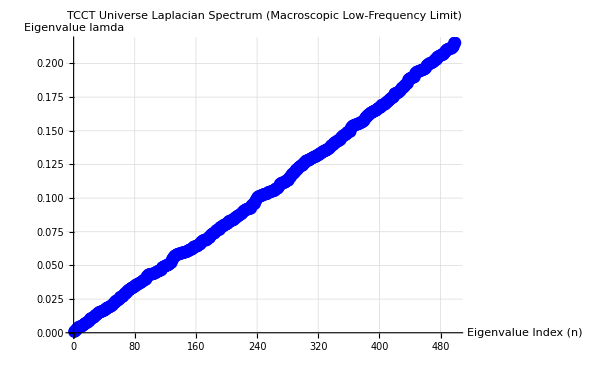

```mathematica
(* ==========================================================*)(*终极拓扑审判：提取 400 步 TCCT 宇宙的拉普拉斯宏观特征谱*)(* ==========================================================*)Print[Style["[1/4] 正在剥离因果方向，构建纯粹的无向拓扑骨架...",Blue,Bold]];
(*将所有边转化为无向边，防止出现虚数特征值*)
undirectedUniverse=Graph[VertexList[universe],UndirectedEdge@@@EdgeList[universe]];

Print[Style["[2/4] 正在构建巨型浮点稀疏矩阵 (Kirchhoff Matrix)...",Blue,Bold]];
(*加 N 强制转换为浮点稀疏矩阵，这是计算 10 万节点不崩的秘诀*)
lapMat=N[KirchhoffMatrix[undirectedUniverse]];

Print[Style["[3/4] 正在对角化本征态，提取宏观极限 (最接近 0 的 500 个能量级)...",Blue,Bold]];
(*-500 表示提取绝对值最小的 500 个特征值*)
eigenVals=Eigenvalues[lapMat,-500];

Print[Style["[4/4] 正在绘制宇宙的拓扑声纹图...",Blue,Bold]];
(*清洗数据：取实部，从小到大排序，剔除绝对零模（孤岛）*)
macroSpectrum=Sort[Select[Re[eigenVals],#>10^-10&]];

(*绘制谱线*)
ListPlot[macroSpectrum,PlotStyle->{Blue,PointSize[0.015]},PlotLabel->Style["TCCT Universe Laplacian Spectrum\n(Macroscopic Low-Frequency Limit)",14,Bold],AxesLabel->{"Eigenvalue Index (n)","Eigenvalue \!\(\*lamda\)"},ImageSize->600,GridLines->Automatic]
```